```mathematica
(*Ниже представлены решения (в том числе и численные, прошу прощения за каламбур) диффуров из кр1*)
```

NDSolve::mxst: Maximum number of 148811 steps reached at the point x == -1.04792.

InterpolatingFunction::dmval: Input value {-9.99959} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
(*№2 вариант I*)
```

```mathematica
ode2={y'[x]==  Exp[x]-x*y[x],y[-1]==1}
```

{y'[x]==ⅇ^x-x y[x],y[-1]==1}

```mathematica
sol2=NDSolve[ode2,y,{x,-20,20}]
```

{{y→InterpolatingFunction[…]}}

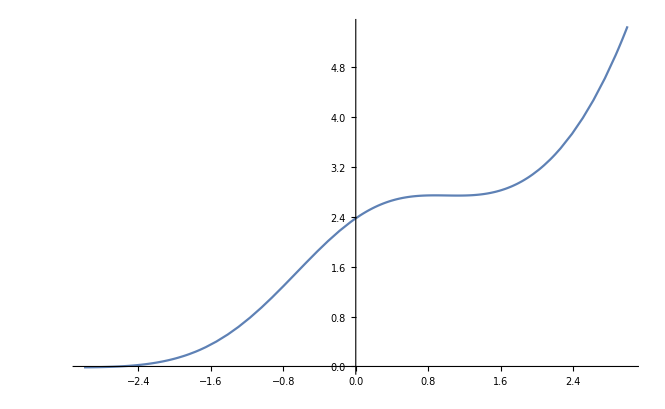

```mathematica
Plot[y[x]/.sol2,{x,-3,3}]
```

```mathematica
DSolve[ode2,y,{x,-20,20}]
```

```mathematica
{{y->Function[{x},1/2 ⅇ^(-1/2-x^2/2) (2 ⅇ+√(2 π) Erfi[(1+x)/(√2)])]}}
(*№2 вариант II*)
```

```mathematica
ode3={y'[x]==  Exp[-x]-x*y[x],y[1]==1}
```

{y'[x]==ⅇ^-x-x y[x],y[1]==1}

```mathematica
sol3=NDSolve[ode3,y,{x,-20,20}]
```

{{y→InterpolatingFunction[…]}}

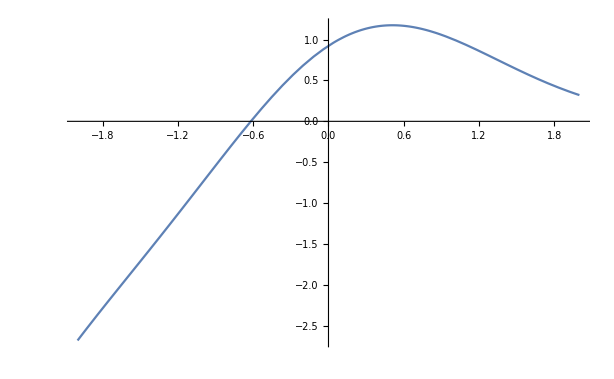

```mathematica
Plot[y[x]/.sol3,{x,-2,2}]
```

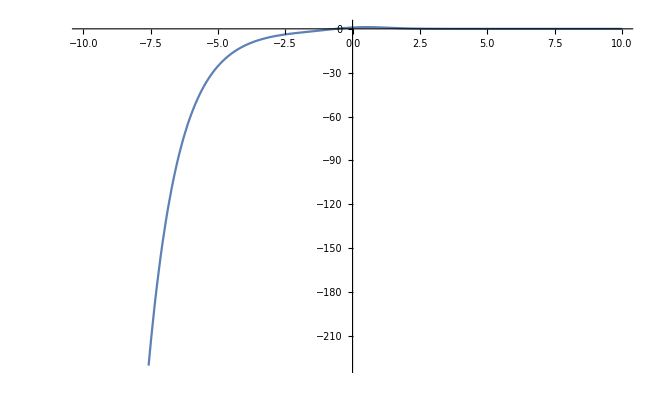
```mathematica
-Graphics-
(*№2 вариант III*)
```

```mathematica
ode4={y'[x]==  Exp[x]+x*y[x],y[1]==1}
```

{y'[x]==ⅇ^x+x y[x],y[1]==1}

```mathematica
sol4=NDSolve[ode4,y,{x,-20,20}]
```

{{y→InterpolatingFunction[…]}}

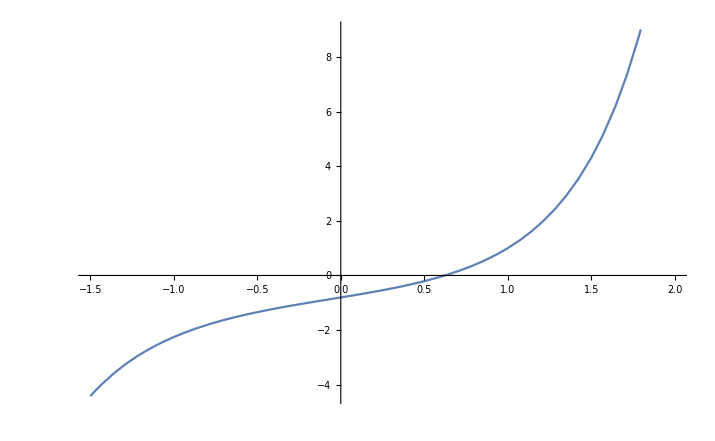

```mathematica
Plot[y[x]/.sol4,{x,-1.5,2}]
```

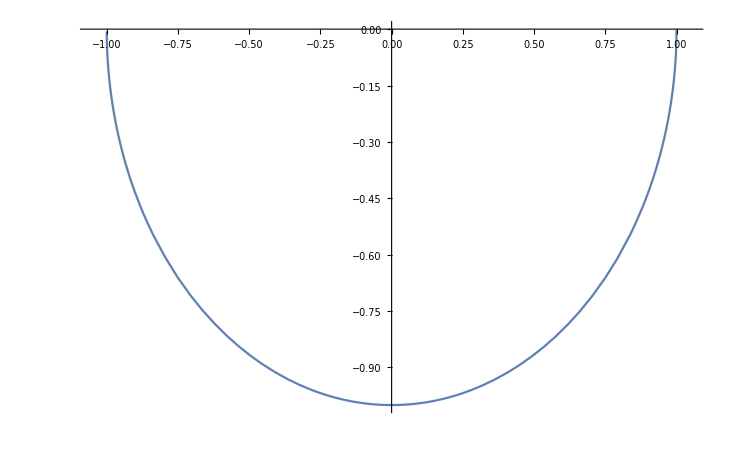

```mathematica
(*#1 варианты I и III*)
Plot[-Sqrt[1-x^2],{x,-1.05,1.05}]
```

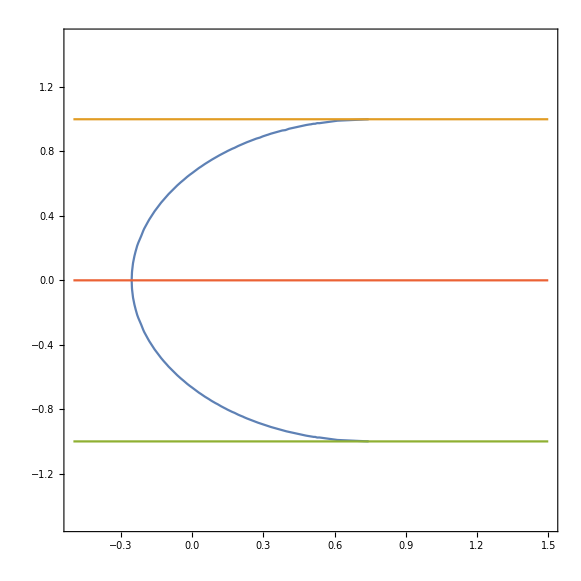

```mathematica
ContourPlot[{-Sqrt[1-y^2]==x-Sqrt[5]/3, y== 1, y== -1, y==  0},{x,-0.5, 1.5},{y,-1.5,1.5}]
```

```mathematica
(*№3 вариант I*)
```

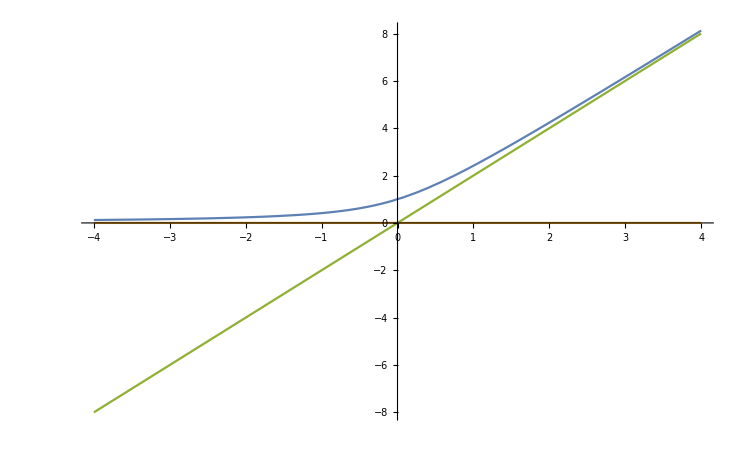

```mathematica
Plot[{ Sqrt[x^2+1]+x, 0 , 2*x},{x,-4,4}]
```

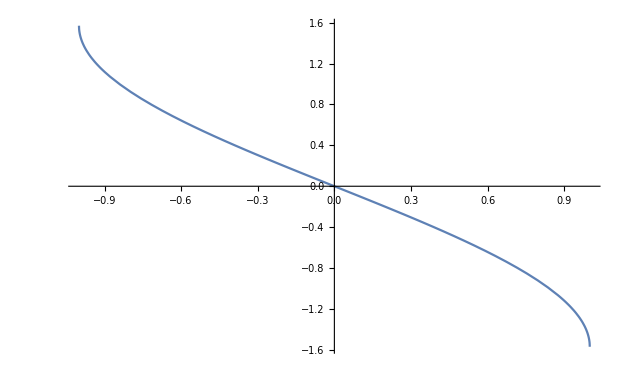

```mathematica
Plot[-ArcSin[x],{x,-1,1}]
```

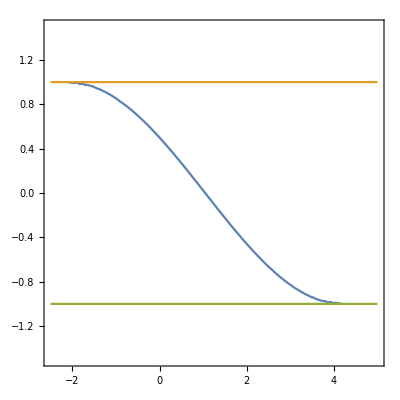

```mathematica
ContourPlot[{ArcSin[y]== -x/2+Pi/6, y== 1, y== -1},{x,-2.5, 5},{y,-1.5,1.5}]
```

```mathematica
ode33={y'[x]== 2*y[x]/(-x+y[x]),y[0]==1}
```

{y'[x]==(2 y[x])/(-x+y[x]),y[0]==1}

```mathematica
sol33=NDSolve[ode33,y,{x,-10,10}]
```

{{y→InterpolatingFunction[…]}}

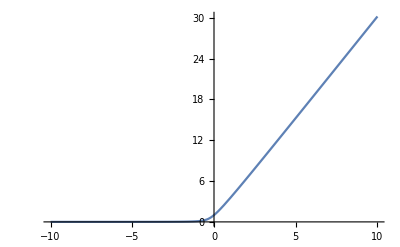

```mathematica
Plot[y[x]/.sol33,{x,-10,10}]
```

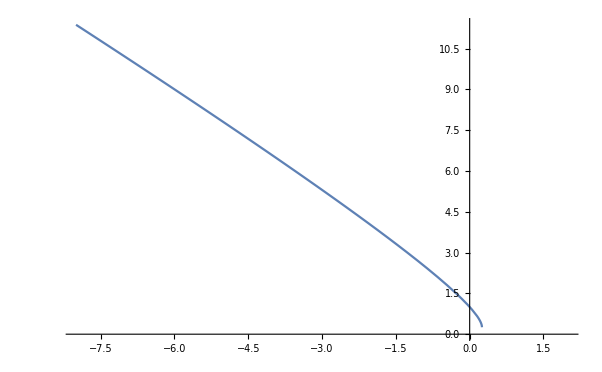

```mathematica
Plot[y[x] = -x+1/2+Sqrt[-x+1/4],{x,-8,2}]
```